Amy Hu
Project 2

```mathematica
Remove["Global`*"]
(* 1 *)

(* Reality *)
SetAttributes[{R1, R2, R3, R4, R5}, Constant];

(* Kirchkoff Current Equations *)
curr1:=ξ==I1 R1+ I3 R3;
curr2:=ξ==I2 R2+I4 R4;
curr3:=ξ==I1 R1+I5 R5+I4 R4;
curr4:=ξ==I2 R2-I5 R5+I3 R3;

(* Kirchkoff Node Equations *)
node1:=I1==I3+I5;
node2:=I2+I5==I4;

(* Set Up + Solve *)
eqnlist = {node1, node2, curr1, curr2, curr3, curr4};
varlist = {I1, I2, I3, I4, I5};
soln = Solve[eqnlist, varlist][[1]]//FullSimplify (*// MatrixForm*);

(* Equivalent Resistance *)
Remf1 = ξ/(I1 + I2)/.soln //FullSimplify;

(* Check *)
soln1 = soln/.R2->R1/.R4->R3//FullSimplify;
Remf2 = ξ/(I1 + I2)/.soln1 //FullSimplify;

(* Print Values *)
Print["1."]
Print["The current through R5 is ", I5 /. soln]
Print["The equivalent resistance seen by the battery is ", Remf1]
Print["\nIf R2 = R1 and R4 = R3, then:"]
Print["The current through R5 is ", I5 /. soln1]
Print["The equivalent resistance seen by the battery is ", Remf2]

(*(* Test *)
soln /.R3-> n R1  /.R4 -> n R2 (* balanced so I5 should = 0 *)*)
```

1.

The current through R5 is ((R2 R3-R1 R4) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))

The equivalent resistance seen by the battery is (R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))/((R1+R2) (R3+R4)+(R1+R2+R3+R4) R5)

If R2 = R1 and R4 = R3, then:

The current through R5 is 0

The equivalent resistance seen by the battery is (R1+R3)/2

```mathematica
Remove["Global`*"]
(* 2 *)
SetAttributes[{R1, R2, R3, R4, R5, ϵ}, Constant];

(* Set Up Matrix and Vectors*)
r = {
{R1,0, R3,0,0},
{0,R2,0,R4,0},
{R1,0,0,R4,R5},
{0,R2,R3,0,-R5},
{1,0,-1,0,-1},
{0,1,0,-1,1}
};
r//MatrixForm;

cur = Transpose[{I1, I2, I3, I4, I5}];
cur//MatrixForm;

v = Transpose[{ξ, ξ, ξ, ξ, 0, 0}];



(* Solve *) 
soln = Solve[r.cur == v, cur][[1]] //FullSimplify;
Print["2."]
Print["The currents through their respective resistors is ", soln//MatrixForm];
Print["The current through R5 is", I5/.soln]
```

2.

The currents through their respective resistors is (I1→((R4 R5+R2 (R3+R4+R5)) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
I2→((R3 R5+R1 (R3+R4+R5)) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
I3→(((R1+R2) R4+(R2+R4) R5) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
I4→((R3 (R2+R5)+R1 (R3+R5)) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))
I5→((R2 R3-R1 R4) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5)))

The current through R5 is((R2 R3-R1 R4) ξ)/(R3 R4 R5+R1 R4 (R3+R5)+R2 R3 (R4+R5)+R1 R2 (R3+R4+R5))

3.

x1[t] = (m1 (t v10+x10)+m2 (-L+t v20+x20)+m2 (L+x10-x20) Cos[√(k (1/m1+1/m2)) t]+(m2 (v10-v20) Sin[√(k (1/m1+1/m2)) t])/(√(k (1/m1+1/m2))))/(m1+m2)

x2[t] = (L m1+m1 t v10+m2 t v20+m1 x10+m2 x20-m1 (L+x10-x20) Cos[√(k (1/m1+1/m2)) t]+(m1 (-v10+v20) Sin[√(k (1/m1+1/m2)) t])/(√(k (1/m1+1/m2))))/(m1+m2)

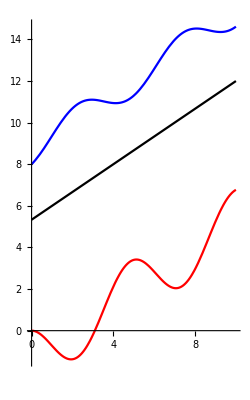

```mathematica
Remove["Global`*"]
(* 3 *)
(* Reality *)
SetAttributes[{m1, m2, k, L}, Constant];
$Assumptions = {Element[{m1, m2, k, L}, Reals] && m1>0 && m2>0 &&k>0 && L>0};

(* Dynamics of the system *)
eqn1 = k(x2[t] - x1[t] - L)==m1 x1''[t] ;
eqn2 = -k(x2[t]-x1[t]- L)==m2 x2''[t];

(* Set up for Solve *)
ellist = {eqn1, eqn2};
iclist = {x1[0]==x10, x2[0]==x20,x1'[0]==v10,x2'[0]==v20};
eqnlist = Join[ellist, iclist];

soln = DSolve[eqnlist, {x1[t], x2[t]}, t][[1]]//FullSimplify;

x1[t_] = x1[t]/.soln;
x2[t_]=x2[t]/.soln;
Print["3."]
Print["x1[t] = ", x1[t]]
Print["x2[t] = ", x2[t]]

(* Constants *)
m1 = 5.;
m2 = 10.;
x10=0;
x20 = 8;
v10=0;
v20=1;
k=5.;
L=10.;

tlo = 0;
thi = 10;

(*Plotting*)
xcm[t_] = (m1 x1[t] + m2 x2[t])/(m1 + m2);

plot1[t_]:=Plot[x1[t], {t, tlo, thi}, PlotStyle -> Red, PlotRange->All];
plot2[t_]:=Plot[x2[t], {t, tlo, thi}, PlotStyle -> Blue, PlotRange->All];
plotcm[t_]:=Plot[xcm[t], {t, tlo, thi}, PlotStyle -> Black, PlotRange->All];

pix[t_] := Show[plot1[t], plot2[t], plotcm[t], PlotRange -> All, AspectRatio->Automatic, Axes->True]

pix[t]
```

```mathematica
Remove["Global`*"]
(* 4 *)

(* Reality *)
SetAttributes[{m1, m2, k, L}, Constant];
$Assumptions = {Element[{m1, m2, k, L}, Reals] && m1>0 && m2>0 &&k>0 && L>0};

(* Dynamics of the system *)
eqn1 = k(x2[t] - x1[t] - L)==m1 x1''[t] ;
eqn2 = -k(x2[t]-x1[t]- L)==m2 x2''[t];

(* Set up for Solve *)
ellist = {eqn1, eqn2};
iclist = {x1[0]==x10, x2[0]==x20,x1'[0]==v10,x2'[0]==v20};
eqnlist = Join[ellist, iclist];

(* Constants *)
m1 = 5;
m2 = 10;
x10=0;
x20 = 8;
v10=0;
v20=1;
k=5;
L=10;

tlo = 0;
thi = 10;

soln = NDSolve[eqnlist, {x1[t], x2[t]}, {t, tlo, thi}][[1]]//FullSimplify;

x1[t_] = x1[t]/.soln;
x2[t_]=x2[t]/.soln;
y1[t]=0;
y2[t]=0;
xcm[t_] = (m1 x1[t] + m2 x2[t])/(m1 + m2);


(*Plotting*)

range = 2 L{{-0.5, 1.5}, {-0.5, 0.5}};

r1[t_] = {x1[t], y1[t]};
r2[t_] = {x2[t], y2[t]};

(* mass 1 *)
block1[t_] := Graphics[
Polygon[{
r1[t],
r1[t] + b{1, 0} ,
r1[t] + b{1, 1},
r1[t] + b{0, 1}
}]]
traj1[t_] := ParametricPlot[r1[t1], {t1, Max[0, t-δ], t}, PlotStyle-> Red]

(* mass 2 *)
block2[t_] := Graphics[
Polygon[{
r2[t],
r2[t] + b{1, 0} ,
r2[t] + b {1, 1},
r2[t] + b{0, 1}
}]]
traj2[t_] := ParametricPlot[r2[t1], {t1,  Max[0, t-δ], t}, PlotStyle-> Blue]

(* "spring" line *)
line[t_] := Graphics[Line[{{x1[t],a}, {x2[t], a}}]];

(*center of mass*)
com[t_] := Graphics[{PointSize[0.015], Point[{xcm[t],a}]}];
traj3[t_] := ParametricPlot[{xcm[t1], 0}, {t1,  Max[0, t-δ], t}, PlotStyle-> Black]

a = 2;
b = 4;
δ=1.5;

pix[t_] := Show[block1[t],block2[t],line[t],com[t], traj1[t], traj2[t], traj3[t], Axes->True, PlotRange->range]
Animate[pix[t], {t, tlo, thi}]
```